# Reproduce Chen 2022 Calculation

```mathematica
Clear[m,s,Coul,kg]
u = 1.66053906660*10^-27 kg;
me = 9.1093837015*10^-31 kg;
c=299792458 m/s;
ϵ0 = 8.85418782 10^-12 (s^2 Coul^2)/(m^3 kg);
ℏ=6.62607004/(2π) 10^-34 (m^2 kg)/s;
kB = 1.3806485 10^-23 kg m^2/s^2 1/Kelvin;
μB=9.274009994*10^-28 kg m^2/s^2 1/G;
a0 = 5.29 10^-11 m;
electroncharge = 1.602 10^-19 Coul;
mSr = 1.46127 10^-25 kg; (*mass of 88Sr*)
cm = .01m;mm=10^-3 m;μm=10^-6 m;nm = 10^-9 m;
THz=10^12 s^-1;GHz=10^9 s^-1;MHz=10^6 s^-1;kHz=10^3 s^-1;
mW = 10^-3 kg m/s^2 m/s;W = kg m/s^2 m/s; μW=10^-6 W;
Tesla = 10000 G;
w0813 = .776μm;
M174plus = 173.938859*u - me;
M171plus = 170.936323*u - me;
R174= 109737.31568160 cm^-1 *M174plus/(M174plus+me);
R171= 109737.31568160 cm^-1 *M171plus/(M171plus+me);
ϵthr = 50443.2 cm^-1;
Inuc = 1/2;
```

```mathematica
μ[n_, mus_] := mus[[1]] + mus[[2]]/(n-mus[[1]])^2+mus[[3]]/(n-mus[[1]])^4
Energy171[n_,mus_]:= (ϵthr -R171/(n-μ[n, mus])^2)
Energy174[n_,mus_]:= (ϵthr -R174/(n-μ[n, mus])^2)
```

## Quantum defect

```mathematica
rawQuantumDefect = Import[NotebookDirectory[]<>"Yb171QuantumDefect.csv"];
QuantumDefects = Association[StringJoin["μ's_",ToExpression[#[[1]]]]->ToExpression[{#[[2]],#[[3]],#[[4]]}]&/@ rawQuantumDefect ]
```

<|μ's_1S0→{4.27837,-5.60943,-258.5},μ's_3S1→{4.4382,6,-18000.},μ's_1P1→{3.95343,-10.5829,728.1},μ's_1D2→{2.71301,-0.929878,-636.4},μ's_3D2→{2.7486,0.0137,-106.55}|>

For visual check try to calculate the energy level of 88Sr from this quantum defects data.

```mathematica
lvls1S0 = Table[{(ToString[n]<>"_1S0"),Energy174[n,QuantumDefects ["μ's_1S0"]]1/cm^-1},{n,6,100}];
lvls3S1 = Table[{(ToString[n]<>"_3S1"),Energy174[n,QuantumDefects ["μ's_3S1"]]1/cm^-1},{n,6,100}];
lvls1P1 = Table[{(ToString[n]<>"_1P1"),Energy174[n,QuantumDefects ["μ's_1P1"]]1/cm^-1},{n,6,100}];
lvls1D2 = Table[{(ToString[n]<>"_1D2"),Energy174[n,QuantumDefects ["μ's_1D2"]]1/cm^-1},{n,6,100}];
lvls3D2 = Table[{(ToString[n]<>"_3D2"),Energy174[n,QuantumDefects ["μ's_3D2"]]1/cm^-1},{n,6,100}];
```

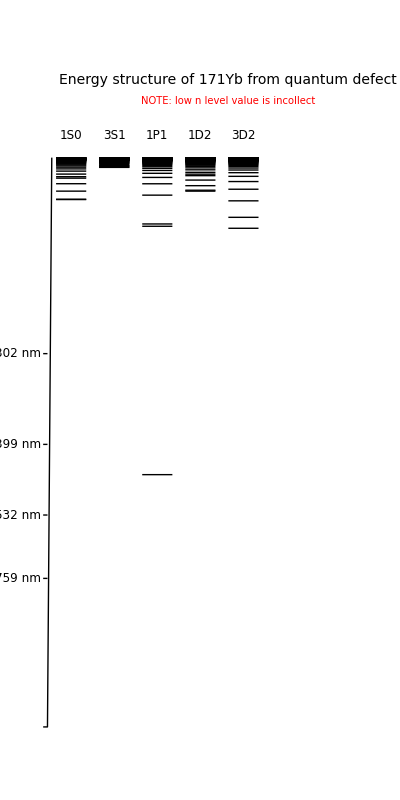

```mathematica
makeLevel[enlist_,J_]:=Line[{{J,#},{J+.7,#}}]&/@enlist[[;;,2]] ;
levelDiag = {makeLevel[lvls1S0,0],makeLevel[lvls3S1,1],makeLevel[lvls1P1,2],makeLevel[lvls1D2,3],makeLevel[lvls3D2,4]};
labellist={"1S0","3S1","1P1","1D2","3D2"};
levelLabels =Table[ {Black,Text[Style[labellist[[ii]],"Label",12],{0.35+ii-1,53000},{0,1}]},{ii,1,Length[labellist]}];
graphicLabel={{Black,Text[Style["Energy structure of 171Yb from quantum defect","Label",14],{4,58000},{0,1}]},
{Red,Text[Style["NOTE: low n level value is incollect","Label",10],{4,56000},{0,2}]}};
scaleinfo={ToString[#]<>" nm",(# nm)^-1 cm}&/@{759,532, 399, 302};
graphicScale={Line[{{-.3,0},{-.2,0},{-.1,50500 }}],Table[{Line[{{-.2,scaleinfo[[ii,2]]},{-.3,scaleinfo[[ii,2]]}}],Text[Style[scaleinfo[[ii,1]],12,"Label",Black],{-.35,scaleinfo[[ii,2]]},{1,0}]},{ii,1,Length[scaleinfo]}]};
levelGraphic=Graphics[{levelDiag ,graphicScale,levelLabels,graphicLabel},AspectRatio->2]
```

## Example calculation for 1S0, 3S1 n=82

```mathematica
μ1S0n82 = μ[82, QuantumDefects ["μ's_1S0"]];
μ3S1n82 = μ[82, QuantumDefects ["μ's_3S1"]];
```

```mathematica
Kin = DiagonalMatrix[Tan/@{π μ1S0n82,π μ3S1n82,π μ3S1n82}] ; Kin //MatrixForm
```

```mathematica
({{1.1915554322135873, 0., 0.}, {0., 5.123265230963444, 0.}, {0., 0., 5.123265230963444}})
```

{{1.19156,0.,0.},{0.,5.12327,0.},{0.,0.,5.12327}}

```mathematica
InOut1[S_,l0_, J_, Inuc_, Ft_, Fbar_] := (-1)^(S+l0+Inuc+Ft) √((2 J +1) (2 Fbar + 1))SixJSymbol[{l0,S,J},{Inuc,Ft,Fbar}];
Out1Out2[Jc_,s0_, S_, Inuc_, Fbar_, Fc_] := (-1)^(s0+Jc+Inuc+Fbar) √((2 S +1) (2 Fc + 1))SixJSymbol[{s0,Jc,S},{Inuc,Fbar,Fc}];
```

```mathematica
Minout1 =DiagonalMatrix[{InOut1[0,0,0,Inuc,1/2,1/2],InOut1[1,0,1,Inuc,1/2,1/2],InOut1[1,0,1,Inuc,3/2,3/2]}]; 
Kout1 = Transpose[Minout1].Kin.Minout1; Kout1 //MatrixForm
```

(1.19156 | 0. | 0.
0. | 5.12327 | 0.
0. | 0. | 5.12327)

```mathematica
Mout1out2 = {{Out1Out2[ 1/2, 1/2, 0, Inuc, 1/2, 0],
Out1Out2[ 1/2, 1/2, 0, Inuc, 1/2, 1],0},
{Out1Out2[ 1/2, 1/2, 1, Inuc, 1/2, 0],Out1Out2[ 1/2, 1/2, 1, Inuc, 1/2, 1],
0},
{0,0,
Out1Out2[ 1/2, 1/2, 1, Inuc, 3/2, 1]}}; Mout1out2//MatrixForm
Kout2 = Transpose[Mout1out2].Kout1.Mout1out2;Kout2//MatrixForm
```

(-1/2 | (√3)/2 | 0
(√3)/2 | 1/2 | 0
0 | 0 | 1)

(4.14034 | 1.70248 | 0.
1.70248 | 2.17448 | 0.
0. | 0. | 5.12327)

```mathematica
K = Kout2[[;;2,;;2]]; K//MatrixForm
```

(4.14034 | 1.70248
1.70248 | 2.17448)

## Find the Solution using the K matrix

```mathematica
Tanpiν2[Eb_] = FullSimplify[DiagonalMatrix[Tan[π √(R171/(# - Eb cm^-1)) ]&/@{-9.482109*0.033357 cm^-1,3.16073*0.033357 cm^-1,3.16073*0.033357 cm^-1}]]
Tanpiν[Eb_] = FullSimplify[DiagonalMatrix[Tan[π √(R171/(# - Eb cm^-1)) ]&/@{-9.482109*0.033357 cm^-1,3.16073*0.033357 cm^-1}]]
```

{{Tan[1040.7 √(-1/(0.316295+1. Eb))],0.,0.},{0.,Tan[1040.7 √(1/(0.105432-1. Eb))],0.},{0.,0.,Tan[1040.7 √(1/(0.105432-1. Eb))]}}

{{Tan[1040.7 √(-1/(0.316295+1. Eb))],0.},{0.,Tan[1040.7 √(1/(0.105432-1. Eb))]}}

```mathematica
Det[K + Tanpiν[Eb]]
```

6.10465+4.14034 Tan[1040.7 √(1/(0.105432-1. Eb))]+2.17448 Tan[1040.7 √(-1/(0.316295+1. Eb))]+Tan[1040.7 √(1/(0.105432-1. Eb))] Tan[1040.7 √(-1/(0.316295+1. Eb))]

6.10465+4.14034 Tan[1040.7 √(1/(0.105432-1. Eb))]+2.17448 Tan[1850.46 √(-1/Eb)]+Tan[1040.7 √(1/(0.105432-1. Eb))] Tan[1040.7 √(-1/(0.316295+1. Eb))]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ν0→-(1.5298×10^9 ν1)/(√(2.3403×10^18+8.99391×10^12 ν1^2))},{ν0→(1.5298×10^9 ν1)/(√(2.3403×10^18+8.99391×10^12 ν1^2))}}

```mathematica
ν1=(1.5298026328198352*^9 ν0)/(√(2.3402960953824993*^18-8.993910004533*^12 ν0^2))
```

(1.5298×10^9 ν0)/(√(2.3403×10^18-8.99391×10^12 ν0^2))

```mathematica
Det[K + DiagonalMatrix[Tan[π #] &/@{-ν0, ν1 }]]
```

6.10465-2.17448 Tan[π ν0]+4.14034 Tan[π ν1]-Tan[π ν0] Tan[π ν1]

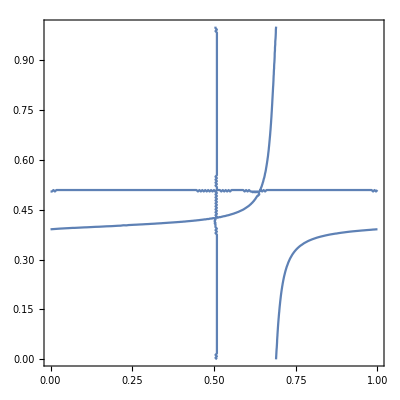

```mathematica
Clear[ν1,ν0]
ContourPlot[Det[K + DiagonalMatrix[Tan[π #] &/@{-ν0, ν1 }]]==0&& ,{ν1, 0,1},{ν0, 0,1}]
```

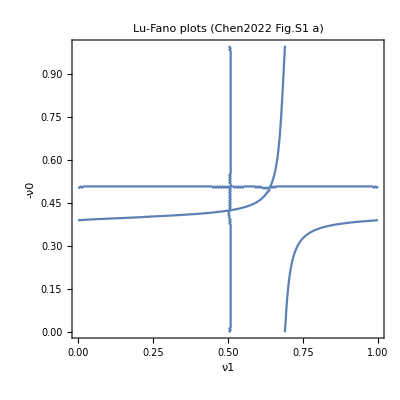

```mathematica
Show[%381,FrameLabel->{{HoldForm[-ν0],None},{HoldForm[ν1],None}},PlotLabel->HoldForm[Lu-Fano plots (Chen2022 Fig. S1 a)],LabelStyle->{GrayLevel[0]}]
```

{{Tan[1040.7 √(-1/(0.316295+1. Eb))],0.},{0.,Tan[1040.7 √(1/(0.105432-1. Eb))]}}

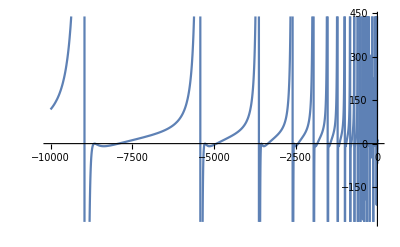

```mathematica
Tanpiν[Eb_] ={{Tan[1040.7018871781286 √(-1/(0.31629470991299996+1. Eb))],0.},{0.,Tan[1040.7018871781286 √(1/(0.10543247061-1. Eb))]}}
Plot[Det[Kout2 + Tanpiν2[Eb]]== -0.001, {Eb, -10000,1}]
```

```mathematica
EnergyListrawA=  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -10000000<Eb<-100},{Eb},Reals] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -100<Eb<-40},{Eb},Reals] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -40<Eb<-30},{Eb},Reals] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -30<Eb<-20},{Eb},Reals] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -20<Eb<-10},{Eb},Reals] ;
EnergyListE = Eb/.EnergyListrawB;

EnergyList = Join[EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE]
```

{-348235.,-348234.,-210368.,-45014.2,-45013.9,-36996.6,-16727.,-16726.7,-14808.,-8652.31,-8651.99,-7920.31,-5274.51,-5274.19,-4921.02,-3548.27,-3547.96,-3351.35,-2549.18,-2548.87,-2428.42,-1919.56,-1919.24,-1840.2,-1497.37,-1497.05,-1442.43,-1200.58,-1200.26,-1160.97,-984.027,-983.709,-954.511,-821.197,-820.879,-798.602,-695.685,-695.367,-677.991,-596.9,-596.581,-582.775,-517.76,-517.441,-506.294,-453.381,-453.061,-443.936,-400.308,-399.988,-392.427,-356.041,-355.72,-349.389,-318.734,-318.412,-313.061,-287.001,-286.679,-282.118,-259.785,-259.461,-255.545,-236.267,-235.943,-232.556,-215.807,-215.482,-212.535,-197.897,-197.57,-194.992,-182.129,-181.801,-179.535,-168.176,-167.847,-165.844,-155.769,-155.438,-153.662,-144.688,-144.356,-142.773,-134.751,-134.417,-133.002,-125.805,-125.47,-124.2,-117.724,-117.386,-116.244,-110.398,-110.059,-109.027,-103.737,-103.396,-102.462,-97.6628,-97.3203,-96.4723,-92.1083,-91.7641,-90.9922,-87.016,-86.6699,-85.9657,-82.3359,-81.988,-81.344,-78.0248,-77.675,-77.0849,-74.0449,-73.6932,-73.1513,-70.3631,-70.0095,-69.5109,-66.9503,-66.5949,-66.1352,-63.7811,-63.4238,-62.9993,-60.8326,-60.4735,-60.0808,-58.085,-57.7242,-57.3603,-55.5204,-55.1578,-54.82,-53.1229,-52.7585,-52.4446,-50.8782,-50.5122,-50.2199,-48.7737,-48.406,-48.1336,-46.798,-46.4287,-46.1744,-44.9406,-44.5698,-44.3321,-43.1924,-42.8201,-42.5977,-41.545,-41.1712,-40.9629,-39.9907,-39.6155,-39.4202,-38.5227,-38.1462,-37.9628,-37.1347,-36.7569,-36.5845,-35.821,-35.4419,-35.2798,-34.5763,-34.1961,-34.0435,-33.3959,-33.0146,-32.8708,-32.2755,-31.8931,-31.7576,-31.2111,-30.8277,-30.6998,-30.1989,-29.8146,-29.6939,-29.2356,-28.8504,-28.7365,-28.3181,-27.9322,-27.8245,-27.4436,-27.0569,-26.9552,-26.6094,-26.2219,-26.1259,-25.8129,-25.4249,-25.3343,-25.0521,-24.6636,-24.578,-24.3247,-23.9358,-23.8551,-23.6288,-23.2396,-23.1636,-22.9626,-22.5732,-22.5018,-22.3244,-21.9349,-21.8681,-21.7125,-21.3233,-21.261,-21.1255,-20.7367,-20.679,-20.5619,-20.1739,-20.1212,-20.0204,-19.6336,-19.5862,-19.4995,-19.1146,-19.0733,-18.9979,-18.6158,-18.5817,-18.5142,-18.1361,-18.1106,-18.0472,-17.6747,-17.6591,-17.5959,-17.2306,-17.2261,-17.1597,-16.8104,-16.8028,-16.7383,-16.4106,-16.3908,-16.3312,-16.0258,-15.9936,-15.9381,-15.6551,-15.6106,-15.5585,-15.2975,-15.2411,-15.1921,-14.9525,-14.8844,-14.8381,-14.6194,-14.5401,-14.4962,-14.2976,-14.2075,-14.1659,-13.9866,-13.8861,-13.8465,-13.6858,-13.5754,-13.5378,-13.3949,-13.2749,-13.2392,-13.1133,-12.9842,-12.9504,-12.8407,-12.7029,-12.6709,-12.5766,-12.4306,-12.4005,-12.3207,-12.1669,-12.1387,-12.0724,-11.9114,-11.8855,-11.8315,-11.6637,-11.6406,-11.5972,-11.4237,-11.4041,-11.369,-11.191,-11.1766,-11.1459,-10.9652,-10.9581,-10.927,-10.7481,-10.7461,-10.7126,-10.5456,-10.5334,-10.503,-10.3495,-10.327,-10.2988,-10.1594,-10.1265,-10.1001}

```mathematica
EnergyList2 = EnergyList  + ϵthr cm ;
EnergyList3 = Partition[EnergyList2,3]*29.979000*10^-3 ;
```

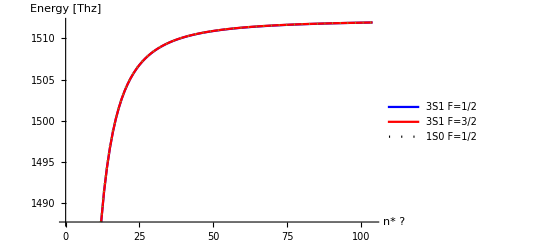

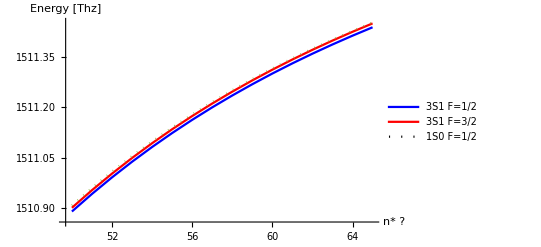

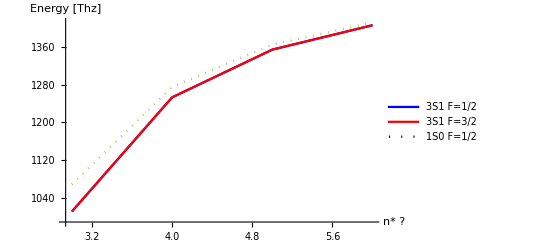

```mathematica
ListLinePlot[{EnergyList3[[;;,1]],EnergyList3[[;;,2]],EnergyList3[[;;,3]]},PlotStyle->{Blue,Red,Dotted},PlotLegends->LineLegend[{Blue,Red,Dotted},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListLinePlot[{EnergyList3[[50;;65,1]],EnergyList3[[50;;65,2]],EnergyList3[[50;;65,3]]},PlotStyle->{Blue,Red,Dotted},PlotLegends->LineLegend[{Blue,Red,Dotted},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{50,65},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListLinePlot[{EnergyList3[[3;;6,1]],EnergyList3[[3;;6,2]],EnergyList3[[3;;6,3]]},PlotStyle->{Blue,Red,Dotted},PlotLegends->LineLegend[{Blue,Red,Dotted},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{3,6},AxesLabel->{"
n* ?","Energy [Thz]"}]
```

```mathematica
li
```

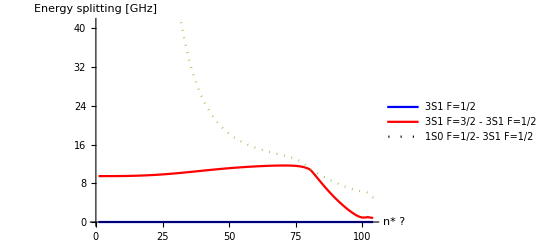

```mathematica
ListLinePlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3,(EnergyList3[[;;,3]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{Blue,Red,Dotted},PlotLegends->LineLegend[{Blue,Red,Dotted},{"3S1 F=1/2","3S1 F=3/2 - 3S1 F=1/2","1S0 F=1/2- 3S1 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy splitting [GHz]"}]
```

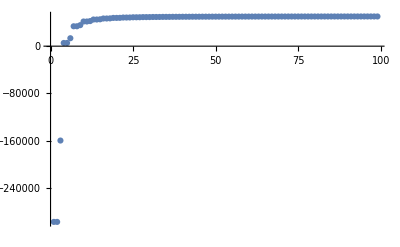

```mathematica
ListPlot[EnergyList2,PlotRange->All]
```

```mathematica
FindRoot
```

```mathematica
"interactive plot"%399DynamicModule[{xc,dx},Manipulate[Plot[Det[K+Tanpiν[Eb]]==0,{Eb,xc-dx,xc+dx}],{{xc,-99/2,"center"},-705/2,507/2},{{dx,50.5,"zoom"},303,3.0300000000000002}],DynamicModuleValues:>{}]
```